# Cálculo dos fatores de segurança e do índice de confiabilidade de revestimento de poço Modos de falha de ruptura (Klever-Stewart), colapso (Klever-Tamano) e escoamento (Von Mises). Poço típico retirado de Rahman & Chilingarian (1995)

## 0. CARACTERÍSTICAS DE POÇO E COMPLETAÇÃO

0.1 Dados com as propriedades dos tubos

```mathematica
(*1 - Outside diameter(in) ;
 2 - Nominal weight(lb/ft) ;
 3 - Grade ;
 4 - Wall thickness (in) ;
 5 - Inside diameter (in);
6 - Pipe collapse resistance (psi);
7 - Body yield strength (1000 lbf) ;
8 - Coupling type ;
 9 - Internal pressure resistance (psi) ;
 10 - Joint strength (1000 lbf);
 11 - Young Modulus (psi) ;
 12 - Poisson Ratio ;
 13 - Yield Strength (psi) ;
 14 - parâmetro n - Klever Stewart;
15 - Joint Strength (lbf) ;*)
```

```mathematica
VMRandomVarsData={{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","DETERM",1.0,0.1},{"Pext","DETERM",1.0,0.1},{"Pint","DETERM",1.0,0.1}};
KSRandomVarsData={{"meKS","NORMAL",1.004,0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","DETERM",1.0,0.1},{"Pext","DETERM",1.0,0.1},{"Pint","DETERM",1.0,0.1}};
KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.09375,0.0333*1.09375},{"Thickness","NORMAL",0.9876,0.002*0.9876},{"Ovality","WEIBULL MIN",0.66,0.2*0.66},{"Excent","WEIBULL MIN",13.2,0.2*13.2},{"Resid. Stress","NORMAL",-0.264,0.2*0.264},{"Nax","DETERM",1.0,0.3},{"Pint","DETERM",1.0,0.3},{"Pext","DETERM",1.0,0.3}};
PipesTable={
{20,       94,   K55,0.438,19.124,520,  1480,LTC,2110,955 ,3.045792621842945 10^7 ,0.28,55000,0.125,955 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{20,       133,K55,0.635,18.730,1500,2125,BTC,3036,2123 ,3.045792621842945 10^7,0.28,55000,0.125,2123 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{20,        65,   K55,0.375,15.250,630,  1012,STC,2260,625 ,3.045792621842945 10^7,0.28,55000,0.125,625 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{16,        75,   K55,0.438,15.124,1020,1178,STC,2630,752 ,3.045792621842945 10^7,0.28,55000,0.125,752 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{16,        84,   L80,0.495,15.010,1480,1929,BTC,4330,1861 ,3.045792621842945 10^7,0.28,80000,0.104,1861 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{16,        109, K55,0.656,14.688,2560,1739,BTC,3950,1895 ,3.045792621842945 10^7,0.28,55000,0.125,1895 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{13.375,98,  L80,0.719,11.937,5910,2800,BTC,7530,2286 ,3.045792621842945 10^7,0.28,80000,0.104,2286 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{13.375,85, P110,0.608,12.159,4690,2682,PTC,8750,2290 ,3.045792621842945 10^7,0.28,110000,0.080,2290 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{13.375,98, P110,0.719,11.937,7280,3145,PTC,10350,2800 ,3.045792621842945 10^7,0.28,110000,0.080,2800 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{9.625, 58.4,L80,0.595,8.435,7890,1350,BTC,8650,1396 ,3.045792621842945 10^7,0.28,80000,0.104,1396 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{9.625, 47,   P110,0.472,8.681,5310,1493,LTC,9449,1213 ,3.045792621842945 10^7,0.28,110000,0.080,1213 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{7,          38,V150,0.540,5.920,19240,1644,EXTL,18900,1430 ,3.045792621842945 10^7,0.28,150000,0.056,1430 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{7,          41,V150,0.590,5.820,22810,1782,PTC,20200,1052 ,3.045792621842945 10^7,0.28,150000,0.056,1052 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{7,          46,V150,0.670,5.660,25970,1999,PTC,25070,1344 ,3.045792621842945 10^7,0.28,150000,0.056,1344 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{7,          38,MW155,0.540,5.920,19700,1697,EXTL,20930,1592 ,3.045792621842945 10^7,0.28,155000,0.050,1592 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{7,          46,SOO140,0.670,5.660,24230,865,PTC,23400,1222 ,3.045792621842945 10^7,0.28,140000,0.060,1222 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData},
{7,          46,SOO155,0.670,5.660,26830,2065,PTC,25910,1344 ,3.045792621842945 10^7,0.28,155000,0.050,1344 10^3,VMRandomVarsData,KSRandomVarsData,KTRandomVarsData}
};
```

0.2 Dados de projeto da completação do poço e métodos de interpolação

```mathematica
SurfaceCasing={
{0,3550.,PipesTable[[5]],12,12},
{3550.,5000.,PipesTable[[6]],12,12}
};
ParticularSurfaceData={(*type*)1,(*Length surface casing*)5000,(*Surface Pressure*)0,(*mud density*){{12,3550},{12,1450}}};
IntermediateCasing={
{0,2000.,PipesTable[[9]],12,12},
{2000.,4000.,PipesTable[[7]],12,12},
{4000.,6400.,PipesTable[[8]],12,12},
{6400.,11100.,PipesTable[[9]],12,12}
};
ParticularIntermediateData={(*type*)2,(*Length Liner casing*)14000,(*Surface Pressure*)5000,(*mud density landing operation  - internal external *){{12,10000},{14,1110}}};
LinerData={
{10500.,12500.,PipesTable[[11]],16.8,16.8},
{12500.,14000.,PipesTable[[10]],16.8,16.8}
};
ParticularLinerData={(*type*)3,(*Length Liner casing*)0,(*Surface Pressure*)5000,(*mud density landing operation  - internal external *){{12,10000},{14,1110}}};
ProductionData={
{0.,3000.,PipesTable[[12]],17.9,17.9},
{3000.,8000.,PipesTable[[15]],17.9,17.9},
{8000.,16000.,PipesTable[[14]],17.9,17.9},
{16000.,19000.,PipesTable[[17]],17.9,17.9}
};

ParticularProductionData={(*type*)4,(*Length Liner casing*)0,(*Surface Pressure*)5000,(*mud density*){{12,10000},{14,1110}}};

LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
x=pt1[[1]]+(y-pt1[[2]])(pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]]);
Return[x]
];

Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]≤Abs[ycoord]≤ Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord];
];
];
];
```

0.3 Janela operacional

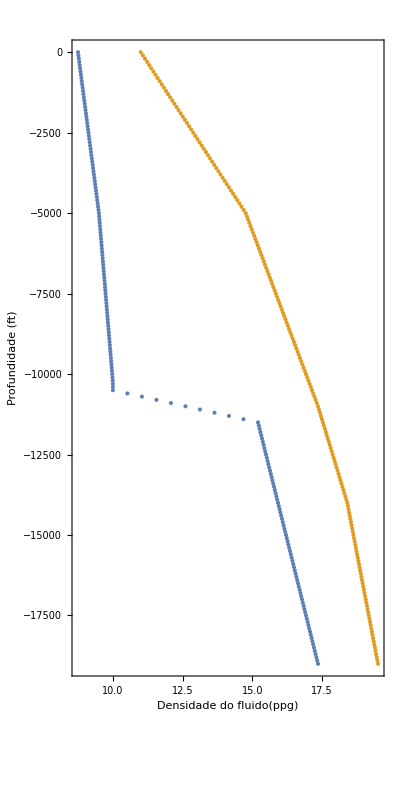

```mathematica
dataporepressure={{8.75,0},{9.5,-5000},{10.,-10250},{10,-10500},{15.2,-11500},{17.35,-19000}};
PtsFracPressure={{11,0},{14.76,-5000},{17.35,-11000},{18.4,-14000},{19.5,-19000}};
tabpore=Table[{Interpolate[y,dataporepressure],y},{y,-19000,0,100}];
tabfrac=Table[{Interpolate[y,PtsFracPressure],y},{y,-19000,0,100}];
ListPlot[{tabpore,tabfrac},AspectRatio->2,Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"Densidade do fluido(ppg)"," Janela Operacional "}},LabelStyle->Directive[Bold,14],Axes->None]
```

## 1 - CÁLCULO DAS TENSÕES E PRESSÕES

1.1  Pressão resistente de Klever Stewart

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},

kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);

puts=(2 kdr t fu)/(de- t);

pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);

Futs=Pi t  fu(de-t);

pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));

pM=pref pfactor;

pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];

If[sa/fu≤ ((√3)/2)^(1-n),
If[pM≤ (pM+0.5^n puts)/2,

pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;

],
pburst=po+pref*pfactorNeck;
];
pburst

]
```

1.2 Cálculo da resistência ao colapso(API BUL. 5C3, 1989)

```mathematica
ComputePipeStrength[siga_,sigy_,d_,t_,young_,nu_]:=Block[{BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(d/t);
dt=d/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);
If[dt≥ range1,
ColapseStrength=(2 young)/(1-nu^2) 1/(dt(dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2≤ dt≤ range1,
ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3≤ dt≤ range2),
ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt≤ range3,
ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}
];
```

1.3 Pressão resistente de Klever Tamano

```mathematica
ComputeColapseResistance[siga_,sigy_,pi_,d_,t_,young_,nu_]:=Block[{ke=1,sol,H=0.22,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4/√3)sigy t/(d-t))^2 (1-(siga/(ky sigy))^2)];
(*deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];*)
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
deltapec=ke (2 young)/(1-nu^2)1/((d/t)(d/t-1)^2);
ColapseStrength=pi+(2 deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4 H deltapy deltapec]);
ColapseStrength

]
```

1.4 Tensão de Von Mises

## Uma vez calculadas as tensões radiais , tangenciais e axiais, procede-se para o cálculo da tensão de von Mises. Para isso monta-se o seguinte tensor de tensões : A tensão de von Mises é dada pela equação onde J2 é o segundo invariante do tensor de tensões deviatórico S : e S é calculado pela equação: sendo I o tensor identidade.

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};
S=sig-1/3 Tr[sig] IdentityMatrix[3];
(*Print[S];*)
J2=1/2 Tr[S.S];
Sqrt[3 J2]
];
```

1.5 Cálculo das tensões radial e tangencial

## O cálculo das tensões radiais e tangenciais é feito através das expressões: onde r é a posição da coordenada radial (r∈[ri,re]), Pi e Po são as pressões internas e externas que atuam no tubular.

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}
];
```

1.6 Cálculo das Pressões internas e externas

## 1.6.1 Cálculos das solicitações de ruptura e de colapso para o revestimento de superfície

```mathematica
BurstSurface[h_,L_,datafracpressure_,densitydata_]:=Block[{PF,Psalt,Pgas,Pburst,eq1,eq2,sol,FracturePressure,hmud,hgas,rhofracatshoe,PI,
rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},

{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];
rhofracatshoe=Interpolate[-L,datafracpressure];
(*Quer que fratura a base da sapata antes da ruptura do tubo na superfície*)
PI=0.052(rhofracatshoe+0.5) L;
Pgas=0.052rhogas (L-h);
Psalt=0.052rhosaltwater h;
Pburst=PI-Pgas-Psalt;
{Pburst,PI-Pgas,Pgas+Psalt}

];

ColapseSurface[h_,L_,dataporepressure_,densitydata_]:=Block[{rhokick,PColapse,
rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];
(*Perda de circulaçao causa a migração do fluido para a fomacao deixando revestimento vazio*)
rhokick=Interpolate[-L,dataporepressure];
PColapse=0.052rhokick h;
{PColapse,0,PColapse}

];
```

## 1.6.2 Cálculos das solicitações de ruptura e de colapso para o revestimento intermediário

```mathematica
ColapseIntermediate[h_,Lliner_,IntermediateData_, dataporepressure_,densitydata_]:=Block[{ha,hm1,hm2,ExtPress,InterPress,Linter,sz,
rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];
sz=Length[IntermediateData];
Linter=IntermediateData[[sz,2]];
hm2= rhosaltwater Lliner/rhoheaviestmud;
ha=Lliner-hm2;
hm1=Linter-ha;
If[h> ( Linter-hm1),
InterPress=0.052 rhoheaviestmud (h-(Linter-hm1));
ExtPress=0.052 rhocurrentmud h;
,
InterPress=0;
ExtPress=0.052 rhocurrentmud h;
];
{ExtPress-InterPress,InterPress,ExtPress}
];
BurstIntermediate[h_,Lliner_,SurfacePressure_,IntermediateData_,datafracpressure_,densitydata_]:=Block[{rhofrac,eq1,eq2,InjectionPress,hmud,hgas,sol,InterPress,ExtPress,Linter,sz,hgi,Ptemp,lasth
,rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];
sz=Length[IntermediateData];
Linter=IntermediateData[[sz,2]];
rhofrac=Interpolate[-Lliner,datafracpressure];
InjectionPress=(rhofrac+0.5) 0.052 Lliner;
eq1=Lliner==hgas+hmud;
eq2=SurfacePressure==InjectionPress-0.052(rhogas hgas+rhoheaviestmud hmud);
sol=Solve[{eq1,eq2},{hmud,hgas}];
hmud=sol[[1,1,2]];
hgas=sol[[1,2,2]];
(*Print[hmud];
Print[hgas];*)
If[h≤ hmud,
(*Print["1"];*)
InterPress=SurfacePressure+0.052(rhoheaviestmud h);
ExtPress=0.052 rhosaltwater h;
,
(*Print["2"];*)
hgi=h-hmud;
Ptemp=SurfacePressure+0.052(rhoheaviestmud hmud);
InterPress=Ptemp+0.052(rhogas hgi);
ExtPress=0.052 rhosaltwater h;
];
(*Print["InterPress =",InterPress];
Print["ExtPress =",ExtPress];*)
{InterPress-ExtPress,InterPress,ExtPress}
]
```

## 1.6.3 Cálculos das solicitações de ruptura e de colapso para o liner

```mathematica
ColapseLiner[h_,LinerData_, dataporepressure_,densitydata_]:=Block[{ExterPress,InternPress,hm2,ha,sz,Lliner,rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];
sz=Length[LinerData];
Lliner=LinerData[[sz,2]];
hm2= rhosaltwater Lliner/rhoheaviestmud;
ha=Lliner-hm2;
ExterPress=0.052rhocurrentmud h;
InternPress=0.052 rhoheaviestmud(h-ha);
{ExterPress-InternPress,InternPress,ExterPress}
]
BurstLiner[h_,LinerData_,SurfacePressure_,datafracpressure_,densitydata_]:=Block[{rhofrac,eq1,eq2,InjectionPress,hmud,hgas,sol,InterPress,ExtPress,Linter,sz,hgi,Ptemp,lasth,Lliner,InternPress,ExterPress,rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];
sz=Length[LinerData];
Lliner=LinerData[[sz,2]];
rhofrac=Interpolate[-Lliner,datafracpressure];
InjectionPress=(rhofrac+0.5) 0.052 Lliner;
eq1=Lliner==hgas+hmud;
eq2=SurfacePressure==InjectionPress-0.052(rhogas hgas+rhoheaviestmud hmud);
sol=Solve[{eq1,eq2},{hmud,hgas}];
hmud=sol[[1,1,2]];
hgas=sol[[1,2,2]];
InternPress=SurfacePressure+hmud rhoheaviestmud 0.052+(h-hmud)rhogas 0.052;
ExterPress=0.052rhosaltwater h;
{InternPress-ExterPress,InternPress,ExterPress}
]
```

## 1.6.4 Cálculos das solicitações de ruptura e de colapso para o revestimento de produção

```mathematica
ColapseProduction[h_,ProductionData_,densitydata_]:=Block[{ExterPress,InternPress,rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];
ExterPress=0.052rhoheaviestmud h;
(*ExterPress=0.052rhoheaviestmud (14000/19000)h;*)
InternPress=0;
{ExterPress-InternPress,InternPress,ExterPress}
]
BurstProduction[h_,ProductionData_,SurfacePressure_,dataporepressure_,densitydata_]:=Block[{rhoformation,Ltotal,sz,InternPress,ExternPress,rhogas,rhosaltwater,rhocurrentmud,rhoheaviestmud},
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}=SetDensityData[densitydata];

sz=Length[ProductionData];
Ltotal=ProductionData[[sz,2]];
rhoformation=Interpolate[-Ltotal,dataporepressure];
InternPress=(rhoformation  Ltotal-rhogas Ltotal)0.052+(rhoheaviestmud h)0.052;
ExternPress=rhosaltwater h 0.052;
{InternPress-ExternPress,InternPress,ExternPress}

]
```

## 1.6.5 Gerenciamento das chamadas de cálculo de ruptura e colapso

```mathematica
ComputeBurst[h_,data_,dataporepress_,datafracpress_,particulardata_,densitydata_]:=Block[{BurstPressure,ColapsePressure,type,L,SurfacePressure,InternalPress,ExternalPress,piburst,picol,poburst,pocol},
type=particulardata[[1]];
L=particulardata[[2]];
SurfacePressure=particulardata[[3]];
Switch[type
,1,
(*Print["type Surface"];*)
{BurstPressure,piburst,poburst}=BurstSurface[h,L,datafracpress,densitydata];
,2,
(*Print["type Intermediate"];*)
{BurstPressure,piburst,poburst}=BurstIntermediate[h,L,SurfacePressure,data,datafracpress,densitydata];
,3,
(*Print["type Liner"];*)
{BurstPressure,piburst,poburst}=BurstLiner[h,data,SurfacePressure,datafracpress,densitydata];
,4,
(*Print["type Production"];*)
{BurstPressure,piburst,poburst}=BurstProduction[h,data,SurfacePressure,dataporepress,densitydata];
];
Return[{BurstPressure,piburst,poburst}]
];
```

```mathematica
ComputeColapse[h_,data_,dataporepress_,datafracpress_,particulardata_,densitydata_]:=Block[{BurstPressure,ColapsePressure,type,L,SurfacePressure,InternalPress,ExternalPress,piburst,picol,poburst,pocol},
type=particulardata[[1]];
L=particulardata[[2]];
SurfacePressure=particulardata[[3]];
Switch[type
,1,
(*Print["type Surface"];*)
{ColapsePressure,picol,pocol}=ColapseSurface[h,L,dataporepress,densitydata];
,2,
(*Print["type Intermediate"];*)
{ColapsePressure,picol,pocol}=ColapseIntermediate[h,L,data, dataporepress,densitydata];
,3,
(*Print["type Liner"];*)
{ColapsePressure,picol,pocol}=ColapseLiner[h,data, dataporepress,densitydata];
,4,
(*Print["type Production"];*)
{ColapsePressure,picol,pocol}=ColapseProduction[h,data,densitydata];
];
Return[{ColapsePressure,picol,pocol}]
]
```

## 1.6.6 Métodos de cálculo dos coeficientes de segurança

```mathematica
ComputeTensionStresses[load_,de_,As_,burstresistance_,pipedata_]:=Block[{weigthft=pipedata[[2]],totalload,Yp=pipedata[[15]],var1,var2},
(*Shock and bending*)
var1=load+weigthft 3200+63 de weigthft 3;
(*Pressure test*)
var2=load+burstresistance 0.6 As;
If[var1>var2,(* Print["(*Shock and bending*)"];*)totalload=var1, (*Print["(*Pressure test*)"];*)totalload=var2];
{Yp,totalload}
]
```

## 1.6.7 Cálculo da tensão axial

```mathematica
ComputeDeltaAxialStress[deltah_,pipedata_]:=Block[{de,di,sigy,young,nu,Wn,t,secarea,deltasiga,deltaload,n},
{de,di,t,sigy,young,nu,Wn,n}=SetData[pipedata]; 
secarea=Pi (de^2 - di^2)/4;
deltaload=Wn deltah;
deltasiga=deltaload/secarea;
{deltasiga,deltaload}
];

GetBoyanceParameters[particulardata_]:=Block[{rho1,rho2,L1,L2},
rho1=particulardata[[4,1,1]];
rho2=particulardata[[4,2,1]];
L1=particulardata[[4,1,2]];
L2=particulardata[[4,2,2]];
{rho1,rho2,L1,L2}
];

ComputeBoyanceForce[pipedata_,particulardata_]:=Block[{rho1,rho2,L1,L2,Fb,Wn,Ao,Ai,de,di,t,young,nu,sigy,pi,po,n},
{de,di,t,sigy,young,nu,Wn,n}=SetData[pipedata];
Ao=Pi/4  de^2;
Ai=Pi/4  di^2;
{rho1,rho2,L1,L2}=GetBoyanceParameters[particulardata];
po=0.052 (rho1 L1+ rho2 L2);
pi=0.052 rho1(L2+L1);
Fb=Ao po-Ai pi;
Fb
];
```

## 1.6.8 Métodos auxiliares

```mathematica
SetDensityData[densitydata_]:=Block[{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud},
rhogas=densitydata[[1]];
rhosaltwater=densitydata[[2]];
rhoheaviestmud=densitydata[[3]];
rhocurrentmud=densitydata[[4]];
{rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud}
];

SetData[currentpipedata_]:=Block[{de,di,t,sigy,young,nu,weigthft,nfactorStewart},
de=currentpipedata[[1]];
di=currentpipedata[[5]];
weigthft=currentpipedata[[2]];
t=currentpipedata[[4]];
sigy=currentpipedata[[13]];
young=currentpipedata[[11]];
nu=currentpipedata[[12]];
nfactorStewart=currentpipedata[[14]];
{de,di,t,sigy,young,nu,weigthft,nfactorStewart}
];
```

## 1.6.9 Gerenciamento dos cálculos

```mathematica
Compute[dataporepressure_,datafracpressure_,data_,particulardata_,globaldensitydata_,steps_]:=Block[{internaldensitydata,sz,L,deltah,h,counter,tabsplited,i,totalweigth=0,de,di,As,siga,Fb,Fap,currentpipedata,t,sigy,young,nu,weigthperfeet,n,rhomudin,ColaspsePressure,picolapse,pocolapse,ColapseResistance,BurstPressure,piburst,poburst,BurstResistance,deltaload,deltasiga,Solution1,Solution2,Solution3,Solution4,Solution5,Solution6,Solution7,Solution8,Solution9,Solution10,Solution11,Solution12,Solution13,Solution14,Solution15,Ai,Ao,Fa,Bucklingforce,AxialForce,ComputeAxialStress,JointResistance,TotalTension,ComputeBucklingAxialStress,SigBoyanceResistance,pi,po,deltasigaw,rhogas,rhosaltwater,rhoheaviestmud,rhocurrentmud,Aup,Alow,deltasigap,sigap,PiBurst={},PoBurst={},PiColapse={},PoColapse={},BSF={},CSF={},AllSolutionburst={},AllSolutioncolapse={},VMStress,SigR,SigTheta,SafetyFactorVecBurst={},SafetyFactorVecColapse={},VMStressBurst,VMStressColapse,KSresistance,KTresistance,VMB={},VMC={}},
internaldensitydata=globaldensitydata;
 sz=Length[data];
L=data[[sz,2]]-data[[1,1]];
deltah=L/steps;
h=data[[1,1]];
counter=1;
tabsplited=Table[0,{sz},{steps}];
For[i=1,i≤sz,i++,totalweigth+=(data[[i,2]]-data[[i,1]]) data[[i,3]][[2]]];
de=data[[1,3]][[1]];
di=data[[1,3]][[5]];
As=Pi (de^2 -di^2)/4;
siga=totalweigth/As;
Fb=ComputeBoyanceForce[data[[1,3]],particulardata];
Fap=0;

For[i=1,i≤steps,i++,

If[h≥ data[[counter,2]],
counter++;
];

currentpipedata=data[[counter,3]];
{de,di,t,sigy,young,nu,weigthperfeet,n}=SetData[currentpipedata];
rhomudin=data[[counter,4]];
internaldensitydata=AppendTo[internaldensitydata,rhomudin];

{ColaspsePressure,picolapse,pocolapse}=ComputeColapse[h,data,dataporepressure,datafracpressure,particulardata,internaldensitydata];
ColapseResistance=ComputeColapseResistance[siga,sigy,picolapse,de,t,young,nu];

{BurstPressure,piburst,poburst}=ComputeBurst[h,data,dataporepressure,datafracpressure,particulardata,internaldensitydata];
BurstResistance=ComputeBurstResistance[n,de,t,1.2sigy,siga,poburst];

AppendTo[PiBurst,{piburst,-h}];
AppendTo[PoBurst,{poburst,-h}];
AppendTo[PiColapse,{picolapse,-h}];
AppendTo[PoColapse,{pocolapse,-h}];

{JointResistance,TotalTension}=ComputeTensionStresses[totalweigth,de,As,BurstResistance,currentpipedata];
internaldensitydata=Delete[internaldensitydata,4];

(*Descida do revestimento *)
Ai=Pi/4  di^2;
Ao=Pi/4  de^2;
As=Ao-Ai;
Fa=totalweigth;
Bucklingforce=Fa-Fb+Fap;
pi=0.052 rhomudin h;
SigBoyanceResistance=pi( Ai- Ao)/As;
sigap=pi (Aup-Alow)/As;
ComputeBucklingAxialStress=Bucklingforce/As;



If[BurstResistance/BurstPressure<10^8 ,
AppendTo[BSF,{BurstResistance/BurstPressure,-h}];
];
If[ColapseResistance/ColaspsePressure<10^8 ,
AppendTo[CSF,{ColapseResistance/ColaspsePressure,-h}];
];
{SigR,SigTheta}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,piburst,poburst];
VMStressBurst=ComputeVonMises[SigR,SigTheta,Fa/(Ai-Ao)];
AppendTo[AllSolutionburst,{sigy/VMStressBurst,-h,piburst,poburst,currentpipedata,Fa/(Ai-Ao),counter,0,weigthperfeet,h}];
AppendTo[VMB,{sigy/VMStressBurst,-h}];
KSresistance=ComputeBurstResistance[n,de,t,sigy,Fa/(Ai-Ao),poburst];
AppendTo[SafetyFactorVecBurst,{KSresistance/(piburst-poburst),-h}];
KTresistance=ComputeColapseResistance[Fa/(Ai-Ao),sigy,picolapse,de,t,young,nu];
AppendTo[SafetyFactorVecColapse,{KTresistance/(pocolapse-picolapse),-h}];

{SigR,SigTheta}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,picolapse,pocolapse];
VMStressColapse=ComputeVonMises[SigR,SigTheta,Fa/(Ai-Ao)];
AppendTo[VMC,{sigy/VMStressColapse,-h}];
AppendTo[AllSolutioncolapse,{sigy/VMStressColapse,-h,picolapse,pocolapse,currentpipedata,Fa/(Ai-Ao),counter,0,weigthperfeet,h}];

deltaload = weigthperfeet*deltah;
deltasiga=deltaload/As;

siga-=deltasiga;
totalweigth-=deltaload;
h+=deltah;
];

{PiBurst,PoBurst,PiColapse,PoColapse,BSF,CSF,AllSolutionburst,AllSolutioncolapse,VMB,VMC,SafetyFactorVecBurst,SafetyFactorVecColapse}
]
```

2 - Cálculo e pós-processamento - Poço exemplo Rahman

## 2.1 Rev. Superfície: casos críticos considerados: “Kick full of gas “ e “Full Evacuation”

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

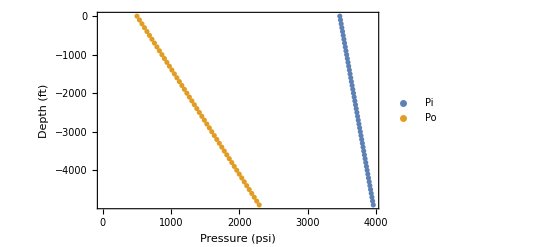

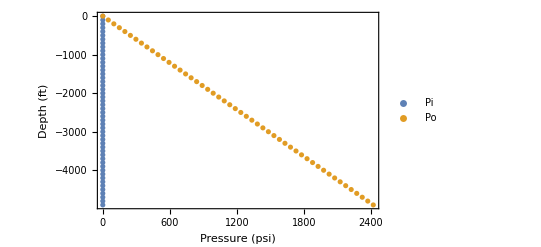

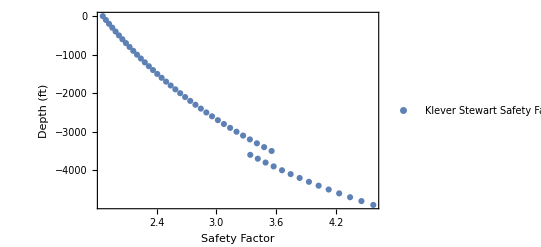

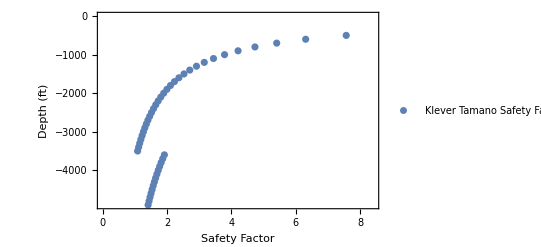

```mathematica
rhogas=0.1/0.052;
rhosaltwater=0.465/0.052;
rhoheaviestmud=17.9;
globaldensitydata={rhogas,rhosaltwater,rhoheaviestmud};
steps=50;

{PiBurst,PoBurst,PiColapse,PoColapse,BSF,CSF,AllSolutionburstSurf,AllSolutioncolapseSurf,VMBSurf,VMCSurf,SafetyFactorVecBurstSurf,SafetyFactorVecColapseSurf}=Compute[dataporepressure,PtsFracPressure,SurfaceCasing,ParticularSurfaceData,globaldensitydata,steps];
ListPlot[{PiBurst,PoBurst},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Kick loading - Partial Full Of Gas"}},PlotLegends->{"Pi","Po"}]
ListPlot[{PiColapse,PoColapse},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Lost Circulation Loading - Full Evacuation"}},PlotLegends->{"Pi","Po"}]
ListPlot[BSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor ","Kick loading - Partial Full Of Gas"}},PlotLegends->{"Klever Stewart Safety Factor"}]
ListPlot[CSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor ","Lost Circulation Loading - Full Evacuation"}},PlotLegends->{"Klever Tamano Safety Factor"}]
(*b=Compute[dataporepressure,PtsFracPressure,SurfaceCasing,ParticularSurfaceData,globaldensitydata,steps];
ListPlot[{b[[1]],b[[4]]},Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"Pressão Solicitante(psi)","  "}},PlotLegends->{" Colapso "," Ruptura "}]
ListPlot[{b[[2]],b[[5]]},Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"Pressão Resistente(psi)","  "}},PlotLegends->{" Colapso "," Ruptura "}]
red=Graphics[{Red,Table[Circle[{0,0},i],{i,3}]}];
black=Graphics[{Black,Table[Circle[{0,0},i],{i,3}]}];
sf=ListPlot[{b[[3]],b[[6]]},Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"Fator de Segurança","  "}},PlotLegends->{" Colapso "," Ruptura "}]*)
```

## 2.2 - Rev. Intermediário, casos críticos considerados: “Kick full of gas “ e “Full Evacuation”

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

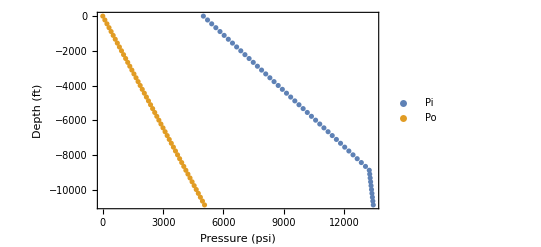

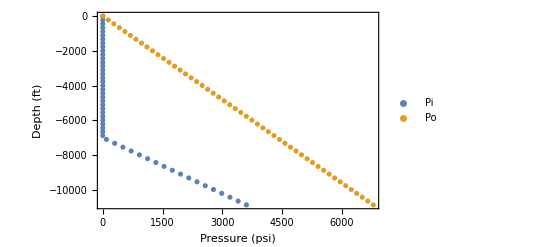

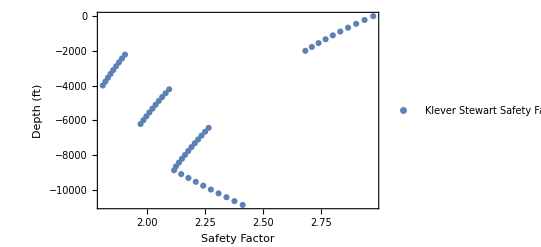

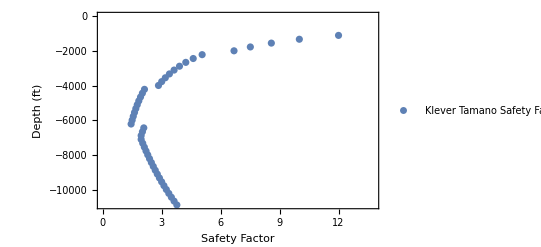

```mathematica
steps=50;
{PiBurst,PoBurst,PiColapse,PoColapse,BSF,CSF,AllSolutionburstInter,AllSolutioncolapseInter,VMBInter,VMCInter,SafetyFactorVecBurstInter,SafetyFactorVecColapseInter}=Compute[dataporepressure,PtsFracPressure,IntermediateCasing,ParticularIntermediateData,globaldensitydata,steps];
ListPlot[{PiBurst,PoBurst},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Kick loading - Partial Full Of Gas"}},PlotLegends->{"Pi","Po"}]
ListPlot[{PiColapse,PoColapse},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Lost Circulation Loading - Full Evacuation"}},PlotLegends->{"Pi","Po"}]
ListPlot[BSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor ","Kick loading - Partial Full Of Gas"}},PlotLegends->{"Klever Stewart Safety Factor"}]
ListPlot[CSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor ","Lost Circulation Loading - Full Evacuation"}},PlotLegends->{"Klever Tamano Safety Factor"}]
```

## 2.3 - Rev. Liner, casos críticos considerados: “Kick full of gas ” e “Full Evacuation”

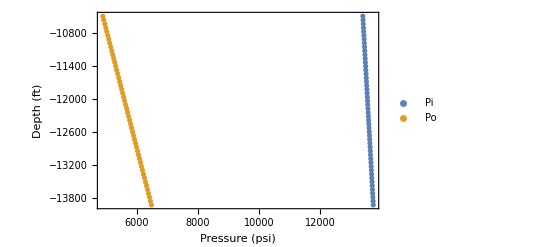

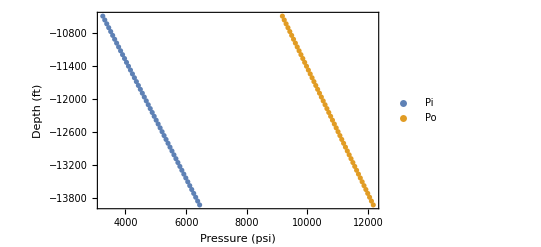

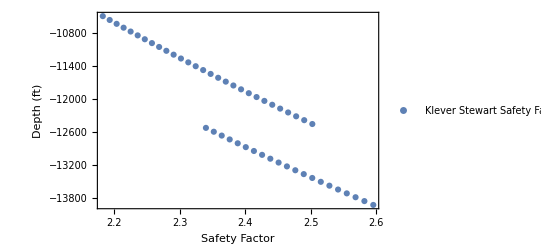

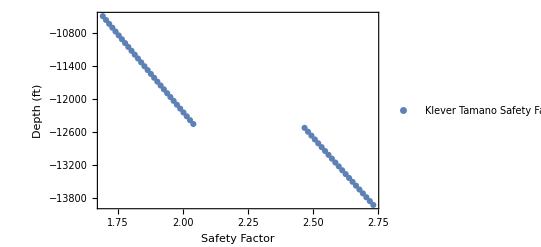

```mathematica
steps=50;
{PiBurst,PoBurst,PiColapse,PoColapse,BSF,CSF,AllSolutionburstLiner,AllSolutioncolapseLiner,VMBLiner,VMCLiner,SafetyFactorVecBurstLiner,SafetyFactorVecColapseLiner}=Compute[dataporepressure,PtsFracPressure,LinerData,ParticularLinerData,globaldensitydata,steps];
ListPlot[{PiBurst,PoBurst},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Kick loading - Partial Full Of Gas"}},PlotLegends->{"Pi","Po"}]
ListPlot[{PiColapse,PoColapse},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Lost Circulation Loading - Full Evacuation"}},PlotLegends->{"Pi","Po"}]
ListPlot[BSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor ","Kick loading - Partial Full Of Gas"}},PlotLegends->{"Klever Stewart Safety Factor"}]
ListPlot[CSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor ","Lost Circulation Loading - Full Evacuation"}},PlotLegends->{"Klever Tamano Safety Factor"}]
```

## 2.4 - Rev. Produção, casos críticos considerados: “tubing leak” e “perda total do packer fluid”

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

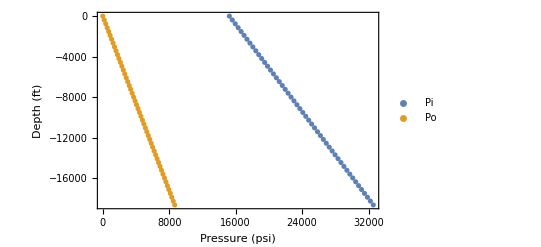

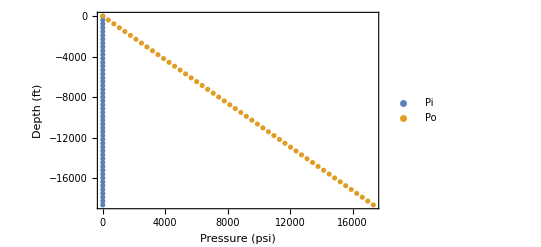

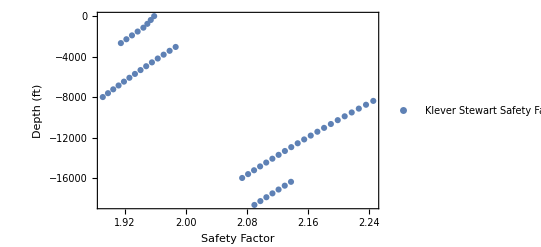

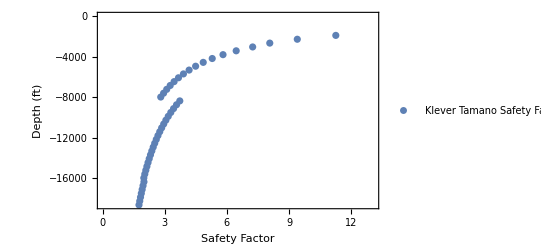

```mathematica
steps=50;
{PiBurst,PoBurst,PiColapse,PoColapse,BSF,CSF,AllSolutionburstProd,AllSolutioncolapseProd,VMBProd,VMCProd,SafetyFactorVecBurstProd,SafetyFactorVecColapseProd}=Compute[dataporepressure,PtsFracPressure,ProductionData,ParticularProductionData,globaldensitydata,steps];
ListPlot[{PiBurst,PoBurst},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Tubing leak"}},PlotLegends->{"Pi","Po"}]
ListPlot[{PiColapse,PoColapse},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)","Total loss of the packer fluid"}},PlotLegends->{"Pi","Po"}]
ListPlot[BSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor ","Tubing leak"}},PlotLegends->{"Klever Stewart Safety Factor"}]
ListPlot[CSF,Frame->True,FrameLabel->{{"Depth (ft)",""},{"Safety Factor "," Total loss of the packer fluid"}},PlotLegends->{"Klever Tamano Safety Factor"}]
```

```mathematica
CreateRVDataVC[tube[[17]]]
```

{{meKS,NORMAL,1.004,0.047188,0.,0.,1.004,0.047188,0.626496,0.875155,1.13285,1.3815,0.},{APIyield,NORMAL,1.1,0.04642,0.,0.,1.1,0.04642,0.72864,0.973252,1.22675,1.47136,0.},{Thickness,NORMAL,1.0069,0.0260787,0.,0.,1.0069,0.0260787,0.79827,0.935693,1.07811,1.21553,0.},{Nax,DETERM,1.,0.1,0.,0.,1.,0.,0.95,0.5,1.5,1.05,0.},{Pext,DETERM,1.,0.1,0.,0.,1.,0.,0.95,0.5,1.5,1.05,0.},{Pint,DETERM,1.,0.1,0.,0.,1.,0.,0.95,0.5,1.5,1.05,0.}}

3.3 Equação de estado limite de Klever-Tamano

## 3.3.1 Vetor gradiente

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{ke=1,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs,sigy];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

```mathematica
ComputeGrad[siga_,sigy_,pint_,pext_,de_,t_,young_,nu_,X1_,X2_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Block[{NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
gx= x1*ComputeColapseStrengthKT[NofD*x7,nYieldStrength*x3,PintofD*x8,nDe,nt*x2,nYoung,nNu,x4,x5,x6]-(PextofD*x9-PintofD*x8);
grad= {{D[gx,x1],D[gx,x2],D[gx,x3],D[gx,x4],D[gx,x5],D[gx,x6],D[gx,x7],D[gx,x8],D[gx,x9]}};
subst={NofD->siga,nYieldStrength->sigy,PintofD->pint,nDe->de,nt->t,nYoung->young,nNu->nu,PextofD->pext,x1->X1,x2->X2,x3->X3,x4->X4,x5->X5,x6->X6,x7->X7,x8->X8,x9->X9};

{{gx},grad}/.subst
];
```

```mathematica
CreateRVDataVC[RVdata_]:=Block[{rvvec={},rvdata,i,RVX={}},

For[i=1,i≤Length[RVdata],i++,
rvdata=Table[0,13];
rvdata[[1]]=RVdata[[i,1]];
rvdata[[2]]=RVdata[[i,2]];
rvdata[[3]]=RVdata[[i,3]];
rvdata[[4]]=RVdata[[i,4]];
AppendTo[RVX, CALCPAR[rvdata]];

];
RVX
]
```

## 3.3.2 Montagem do problema

```mathematica
SolVector={};
IndiceConfiabilidade[data_,revestimento_]:=Block[{CsVsBeta},
CsVsBeta={};
For[w=1,w≤Length[data],w++,
PintofD = data[[w]][[3]]; (* Nominal Internal Pressure at depth D in psi *)
PextofD = data[[w]][[4]]; (* Nominal External Pressure at depth D in psi *)
NofD=data[[w]][[6]] ; (* Nominal Axial Load at depth D in psi*)

selectedTube =ToString[ data[[w]][[5]][[3]] data[[w]][[5]][[2]]  "lb/ft" ];

tube=data[[w]][[5]];

nDe=tube[[1]]; nt=tube[[4]]; nBurstStrength=tube[[9]];
nYoung=tube[[11]]; nNu=tube[[12]]; nYieldStrength=tube[[13]]; KSnfactor= tube[[14]];

ka=2; aN=0.05 nt;  tmin=mint nt;

nUltimateStrength= 1.1875 nYieldStrength;

KTRandomVars=tube[[18]];
NRV=Length[KTRandomVars];
RVX=CreateRVDataVC[KTRandomVars];

NLS = 1;

NP = 20;
CDFLIMPLOT=10^-2.5;
PRINT = False;
ClearAll[vx,fx,GX,GRADX,X1,X2,X3,X4,X5,X6,X7,X8,X9];

SetLimitStateVectors[NRV];

DesignPoint = Table[DPCREATE,{NLS}];
LSPARALLEL = False;
BuildRVParameterVectors[RVX];

GX[fx]:=ComputeGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[1]];
GRADX[fx]:=ComputeGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[2]];


GAUSSIAN = True;
Do[If[TYPE[[i]]≠ "NORMAL"&&TYPE[[i]]≠ "DETERM",
GAUSSIAN = False],{i,1,NRV}];

RX=IdentityMatrix[NRV];

If[Det[RX]== 1,CORRELATED =False,CORRELATED = True];

cov = Table[RX[[i,j]]*SDEV[[i]]*SDEV[[j]],{i,1,NRV},{j,1,NRV}];

ClearAll[Jyz,Jzy,Jzx,Jxz,Jxy,Jyx];

{Jyz,Jzy} = JacobYZ[RX];
{Jxz,Jzx} = JacobXZ[RVX,MEAN];

Jyx = Jyz.Jzx;
Jxy = Jxz.Jzy;

(* 4. Busca pelo ponto de projeto e índice de confiabilidade *)

ConvergenceCrit = {100,"DELTA_BETA",10^-3,0,0};

xh = Table[0,{NLS}];
yh = Table[0,{NLS}];
vg = Table[0,{NLS}];

Do[
FindDesignPoint[lsn];
,{lsn,1,NLS}];

BETA = DPGET[DesignPoint[[1]],{"BETA"}];
ALFA = DPGET[DesignPoint[[1]],{"ALFA"}];

(*AppendTo[SolVector,{revestimento,-data[[w]][[2]],selectedTube,PextofD,PintofD,NofD,data[[w]][[1]],BETA}];*)
AppendTo[CsVsBeta,{BETA,data[[w]][[2]]}];
];
CsVsBeta
];
```

## 3.3.3 Resultados para Klever-Tamano

Revestimento Superfície

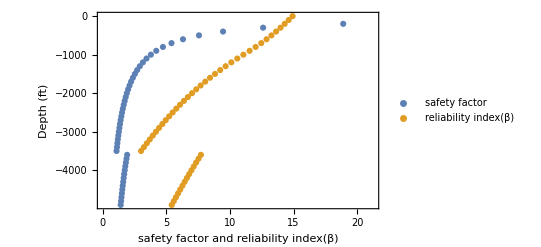

Intermediário Revestimento

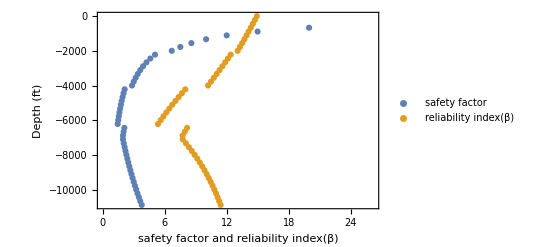

Liner

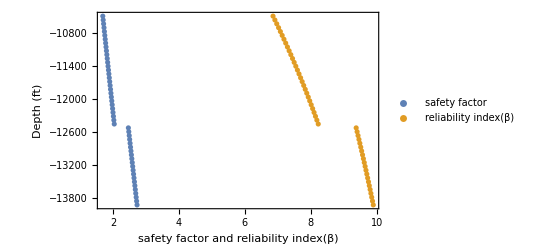

Produção Revestimento

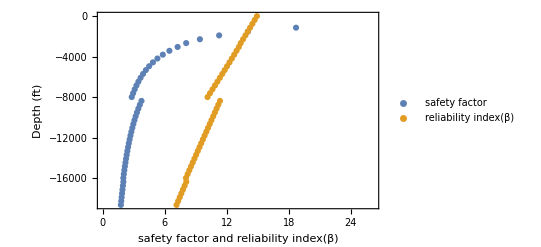

```mathematica
Revestimento Superfície
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseSurf,"Intermediate"];
ListPlot[{SafetyFactorVecColapseSurf,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano"}},PlotLegends->{"safety factor","reliability index(β)"}]

Revestimento Intermediário
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseInter,"Intermediate"];
ListPlot[{SafetyFactorVecColapseInter,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Intermediate Casing"},{"safety factor and reliability index(β) ","Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano"}},PlotLegends->{"safety factor","reliability index(β)"}]


Liner
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseLiner,"Intermediate"];
ListPlot[{SafetyFactorVecColapseLiner,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Liner"},{"safety factor and reliability index(β) ","Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano "}},PlotLegends->{"safety factor","reliability index(β)"}]

Revestimento Produção
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseProd,"Intermediate"];
ListPlot[{SafetyFactorVecColapseProd,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Production Casing"},{"safety factor and reliability index(β) ","Critical Case: Tubing Leak- Assumption: empty - Failure check: Klever-Tamano"}},PlotLegends->{"safety factor","reliability index(β)"}]
```

3.2 Equação de estado limite de Klever-Stewart

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
pBurstKS

];
```

```mathematica
ComputeGrad[n_,de_,t_,fu_,sa_,pi_,po_,X1_,X2_,X3_,X4_,X5_,X6_]:=Block[{NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
gx= x1*ComputeBurstResistance[n,x4*de,x2*t,x3*fu,sa,x5*po]-x6 pi;
grad= {{D[gx,x1],D[gx,x2],D[gx,x3],D[gx,x4],D[gx,x5],D[gx,x6]}};
subst={x1->X1,x2->X2,x3->X3,x4->X4,x5->X5,x6->X6};

{{gx},grad}/.subst
];
```

## 3.2.2 Montagem do problema

```mathematica
IndiceConfiabilidade[data_,revest_]:=Block[{CsVsBeta,KSRandomVars},

CsVsBeta={};
For[w=1,w≤Length[data],w++,
PintofD = data[[w]][[3]]; (* Nominal Internal Pressure at depth D in psi *)
PextofD = data[[w]][[4]]; (* Nominal External Pressure at depth D in psi *)
NofD=data[[w]][[6]] ; (* Nominal Axial Load at depth D in psi*)

selectedTube =ToString[ data[[w]][[5]][[3]] data[[w]][[5]][[2]]  "lb/ft" ];

tube=data[[w]][[5]];

nDe=tube[[1]]; nt=tube[[4]]; nBurstStrength=tube[[9]];
nYoung=tube[[11]]; nNu=tube[[12]]; nYieldStrength=tube[[13]]; KSnfactor= tube[[14]];

KSRandomVars=tube[[17]];
NRV=Length[KSRandomVars];
RVX=CreateRVDataVC[KSRandomVars];

nUltimateStrength= 1.1875 nYieldStrength;
NLS = 1;

NP = 20;
CDFLIMPLOT=10^-2.5;
PRINT = False;
ClearAll[vx,fx,GX,GRADX,X1,X2,X3,X4,X5,X6];

SetLimitStateVectors[NRV];

DesignPoint = Table[DPCREATE,{NLS}];

LSPARALLEL = False;
BuildRVParameterVectors[RVX];

GX[fx] :=ComputeGrad[KSnfactor,nDe,nt*X2,nUltimateStrength*X3,NofD*X4,PintofD*X6,PextofD*X5,X1,X2,X3,X4,X5,X6][[1]];
GRADX[fx] := ComputeGrad[KSnfactor,nDe,nt*X2,nUltimateStrength*X3,NofD*X4,PintofD*X6,PextofD*X5,X1,X2,X3,X4,X5,X6][[2]];

GAUSSIAN = True;
Do[If[TYPE[[i]]≠ "NORMAL"&&TYPE[[i]]≠ "DETERM",
GAUSSIAN = False],{i,1,NRV}];

RX=IdentityMatrix[NRV];

If[Det[RX]== 1,CORRELATED =False,CORRELATED = True];

cov = Table[RX[[i,j]]*SDEV[[i]]*SDEV[[j]],{i,1,NRV},{j,1,NRV}];

ClearAll[Jyz,Jzy,Jzx,Jxz,Jxy,Jyx];

{Jyz,Jzy} = JacobYZ[RX];
{Jxz,Jzx} = JacobXZ[RVX,MEAN];

Jyx = Jyz.Jzx;
Jxy = Jxz.Jzy;

(* 4. Busca pelo ponto de projeto e índice de confiabilidade *)

ConvergenceCrit = {100,"DELTA_BETA",10^-3,0,0};

xh = Table[0,{NLS}];
yh = Table[0,{NLS}];
vg = Table[0,{NLS}];

Do[
FindDesignPoint[lsn];
,{lsn,1,NLS}];

BETA = DPGET[DesignPoint[[1]],{"BETA"}];
ALFA = DPGET[DesignPoint[[1]],{"ALFA"}];

AppendTo[CsVsBeta,{BETA,data[[w]][[2]]}];
];
CsVsBeta
];
```

Revestimento Superfície

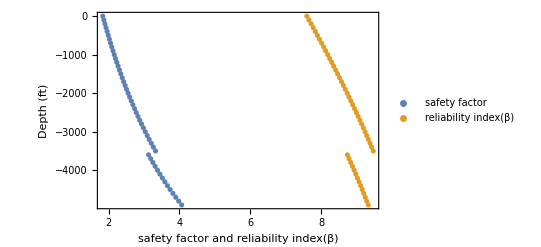

Revestimento Intermediário

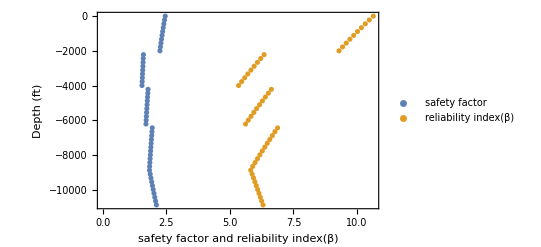

Liner

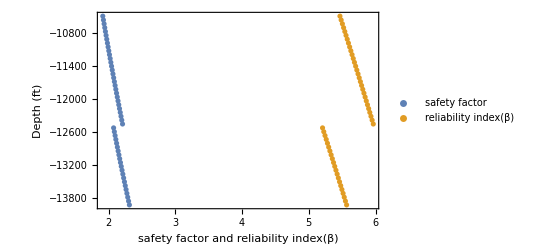

Revestimento Produção

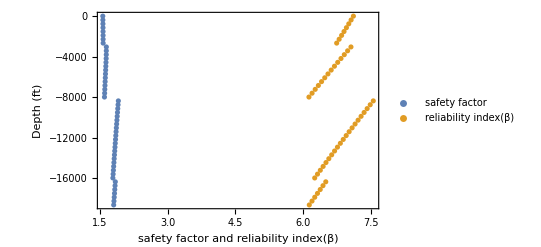

```mathematica
Print[""]
Print["Revestimento Superfície"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstSurf,"Intermediate"];
ListPlot[{SafetyFactorVecBurstSurf,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Stewart"}},PlotLegends->{"safety factor","reliability index(β)"}]

Print[""]
Print["Revestimento Intermediário"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstInter,"Intermediate"];
ListPlot[{SafetyFactorVecBurstInter,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Intermediate Casing"},{"safety factor and reliability index(β) ","Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Stewart"}},PlotLegends->{"safety factor","reliability index(β)"}]


Print[""]
Print["Liner"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstLiner,"Intermediate"];
ListPlot[{SafetyFactorVecBurstLiner,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Liner"},{"safety factor and reliability index(β) ","Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Stewart "}},PlotLegends->{"safety factor","reliability index(β)"}]

Print[""]
Print["Revestimento Produção"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstProd,"Intermediate"];
ListPlot[{SafetyFactorVecBurstProd,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Production Casing"},{"safety factor and reliability index(β) ","Critical Case: Tubing Leak- Assumption: empty - Failure check: Klever-Stewart"}},PlotLegends->{"safety factor","reliability index(β)"}]
```

3.1 Equação de estado limite de von Mises

## 3.1.1 Montagem do problema

```mathematica
IndiceConfiabilidade[data_,revest_]:=Block[{CsVsBeta,w,PintofD,PextofD,siga,tube,de,di,Pib,Pob,nu,sigy,t,selectedTube},
VM[de_,t_,Pib_,Pob_,siga_]:=1/2 √(1/((de-t)^2 t^2)(de^4 (Pib-Pob)^2-2 de^3 (Pib-Pob) (Pib+siga) t+2 de^2 (Pib+siga) (3 Pib-Pob+2 siga) t^2-8 de (Pib+siga)^2 t^3+4 (Pib+siga)^2 t^4));
CsVsBeta={};
For[w=1,w≤Length[data],w++,

siga=data[[w]][[6]] ; (* Nominal Axial Load at depth D in psi*)
tube=data[[w]][[5]];
de=tube[[1]];
di=tube[[5]];
Pib=data[[w]][[3]];
Pob = data[[w]][[4]];
nu=0.30;
sigy=tube[[13]];
t=tube[[4]];

selectedTube =ToString[ data[[w]][[5]][[3]] data[[w]][[5]][[2]]  "lb/ft" ];
RVVec=CreateRVDataVC[tube[[16]]];

NRV =Length[RVVec]+1;
NLS = 1;

NP = 20;
CDFLIMPLOT=10^-2.5;
PRINT = False;

ClearAll[RVX];
RVX = Table[0,{NRV}];


RmeKS = CALCPAR[{"meKS","DETERM",1.004,0.047*1.004,0,0,0,0,0,0,0,0,0}];
RyieldE = CALCPAR[RVVec[[1]]];
RtE= CALCPAR[RVVec[[2]]];

RVX[[1]] = RmeKS;
RVX[[2]] = RtE;
RVX[[3]] = RyieldE;
RVX[[4]] = CALCPAR[RVVec[[3]]];
RVX[[5]] = CALCPAR[RVVec[[4]]];
RVX[[6]] = CALCPAR[RVVec[[5]]];

ClearAll[vx,fx,GX,GRADX,X1,X2,X3,X4,X5,X6];

SetLimitStateVectors[NRV];

DesignPoint = Table[DPCREATE,{NLS}];

LSPARALLEL = False;

(*GX[fx] :={1/2 X1 √((de^4 (Pib-Pob)^2-2 de^3 (Pib-Pob) (Pib+siga) t X2+2 de^2 (Pib+siga) (3 Pib-Pob+2 siga) t^2 X2^2-8 de (Pib+siga)^2 t^3 X2^3+4 (Pib+siga)^2 t^4 X2^4)/(t^2 X2^2 (de-t X2)^2))-sigy X3};*)
GX[fx] :={X1*VM[de,X2*t,X6 Pib,X5 Pob,X4 siga]-sigy X3};
BuildRVParameterVectors[RVX];

GRADX[fx] :={{1/2 √(1/(t^2 X2^2 (de-t X2)^2)(de^4 (Pob X5-Pib X6)^2+2 de^3 t X2 (Pob X5-Pib X6) (siga X4+Pib X6)-8 de t^3 X2^3 (siga X4+Pib X6)^2+4 t^4 X2^4 (siga X4+Pib X6)^2+2 de^2 t^2 X2^2 (siga X4+Pib X6) (2 siga X4-Pob X5+3 Pib X6))),(de^2 X1 (de-2 t X2) (Pob X5-Pib X6) (de^2 (Pob X5-Pib X6)+de t X2 (siga X4+Pib X6)-t^2 X2^2 (siga X4+Pib X6)))/(2 t^2 X2^3 (-de+t X2)^3 √((de^4 (Pob X5-Pib X6)^2+2 de^3 t X2 (Pob X5-Pib X6) (siga X4+Pib X6)-8 de t^3 X2^3 (siga X4+Pib X6)^2+4 t^4 X2^4 (siga X4+Pib X6)^2+2 de^2 t^2 X2^2 (siga X4+Pib X6) (2 siga X4-Pob X5+3 Pib X6))/(t^2 X2^2 (de-t X2)^2))),-sigy,(siga X1 (-4 de siga t X2 X4+4 siga t^2 X2^2 X4-de^2 Pob X5+Pib (de-2 t X2)^2 X6))/(2 t X2 (-de+t X2) √((de^4 (Pob X5-Pib X6)^2+2 de^3 t X2 (Pob X5-Pib X6) (siga X4+Pib X6)-8 de t^3 X2^3 (siga X4+Pib X6)^2+4 t^4 X2^4 (siga X4+Pib X6)^2+2 de^2 t^2 X2^2 (siga X4+Pib X6) (2 siga X4-Pob X5+3 Pib X6))/(t^2 X2^2 (de-t X2)^2))),(de^2 Pob X1 (de^2 (Pob X5-Pib X6)+de t X2 (siga X4+Pib X6)-t^2 X2^2 (siga X4+Pib X6)))/(2 t^2 X2^2 (de-t X2)^2 √((de^4 (Pob X5-Pib X6)^2+2 de^3 t X2 (Pob X5-Pib X6) (siga X4+Pib X6)-8 de t^3 X2^3 (siga X4+Pib X6)^2+4 t^4 X2^4 (siga X4+Pib X6)^2+2 de^2 t^2 X2^2 (siga X4+Pib X6) (2 siga X4-Pob X5+3 Pib X6))/(t^2 X2^2 (de-t X2)^2))),(Pib X1 (de^3 t X2 (-siga X4+Pob X5-2 Pib X6)-8 de t^3 X2^3 (siga X4+Pib X6)+4 t^4 X2^4 (siga X4+Pib X6)+de^4 (-Pob X5+Pib X6)+de^2 t^2 X2^2 (5 siga X4-Pob X5+6 Pib X6)))/(2 t^2 X2^2 (de-t X2)^2 √(1/(t^2 X2^2 (de-t X2)^2)(de^4 (Pob X5-Pib X6)^2+2 de^3 t X2 (Pob X5-Pib X6) (siga X4+Pib X6)-8 de t^3 X2^3 (siga X4+Pib X6)^2+4 t^4 X2^4 (siga X4+Pib X6)^2+2 de^2 t^2 X2^2 (siga X4+Pib X6) (2 siga X4-Pob X5+3 Pib X6))))}};

GAUSSIAN = True;
Do[If[TYPE[[i]]≠ "NORMAL"&&TYPE[[i]]≠ "DETERM",
GAUSSIAN = False],{i,1,NRV}];

RX=IdentityMatrix[NRV];

If[Det[RX]== 1,CORRELATED =False,CORRELATED = True];

cov = Table[RX[[i,j]]*SDEV[[i]]*SDEV[[j]],{i,1,NRV},{j,1,NRV}];

ClearAll[Jyz,Jzy,Jzx,Jxz,Jxy,Jyx];

{Jyz,Jzy} = JacobYZ[RX];
{Jxz,Jzx} = JacobXZ[RVX,MEAN];

Jyx = Jyz.Jzx;
Jxy = Jxz.Jzy;

(* 4. Busca pelo ponto de projeto e índice de confiabilidade *)

ConvergenceCrit = {100,"DELTA_BETA",10^-3,0,0};

xh = Table[0,{NLS}];
yh = Table[0,{NLS}];
vg = Table[0,{NLS}];

Do[
FindDesignPoint[lsn];
,{lsn,1,NLS}];

BETA = DPGET[DesignPoint[[1]],{"BETA"}];
ALFA = DPGET[DesignPoint[[1]],{"ALFA"}];

(*Print["Indice de confiabilidade = ",BETA];
Print["Fatores de Sensibilidade = ",TableForm[Transpose[{NAME,ALFA}]]];*)
AppendTo[CsVsBeta,{BETA,data[[w]][[2]]}];
];
CsVsBeta
];
```

Revestimento Superfície

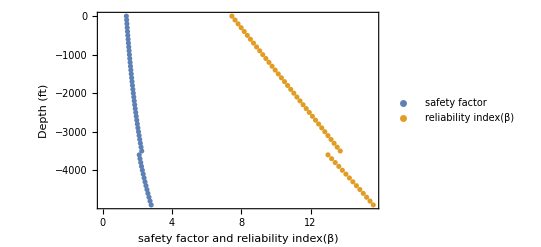

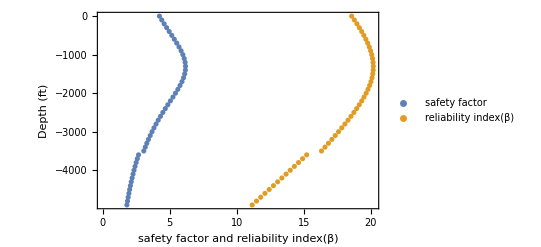

Revestimento Intermediário

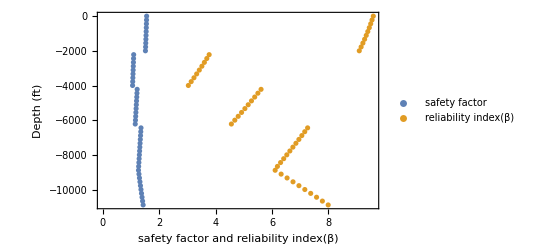

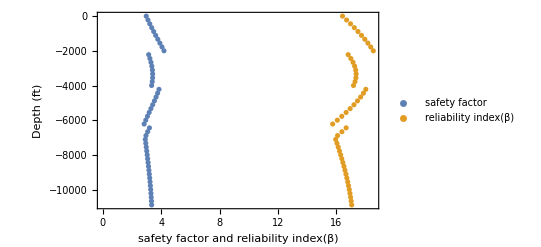

Liner

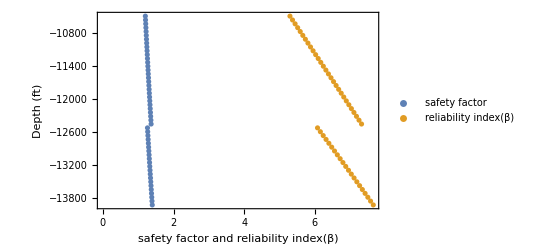

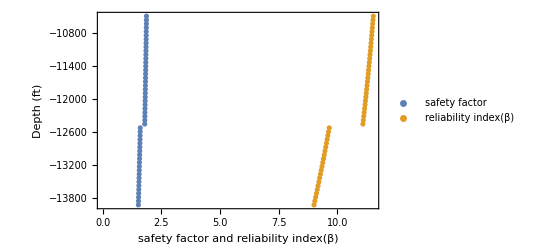

Revestimento Produção

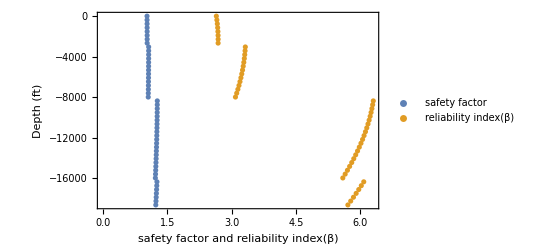

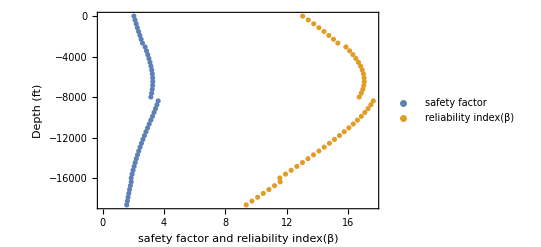

```mathematica
Print["Revestimento Superfície"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstSurf,"Intermediate"];
ListPlot[{VMBSurf,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: von Mises"}},PlotLegends->{"safety factor","reliability index(β)"}]
(*print=BuildTable[SolVector];
TableForm[print];*)
SolVector={};
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseSurf,"Intermediate"];
ListPlot[{VMCSurf,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β)","  Critical Case: Lost Circulation - Assumption: Partial full of fluid - Failure check: von Mises"}},PlotLegends->{"safety factor","reliability index(β)"}]

Print[""]
Print["Revestimento Intermediário"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstInter,"Intermediate"];
ListPlot[{VMBInter,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Intermediate Casing"},{"safety factor and reliability index(β) ","Critical Case: Kick - Assumption: Partial full of gas - Failure check: von Mises"}},PlotLegends->{"safety factor","reliability index(β)"}]
(*print=BuildTable[SolVector];
TableForm[print];*)
SolVector={};
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseInter,"Intermediate"];
ListPlot[{VMCInter,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Intermediate Casing"},{"safety factor and reliability index(β)"," Critical Case: Lost Circulation - Assumption: Partial full of fluid - Failure check: von Mises "}},PlotLegends->{"safety factor","reliability index(β)"}]

Print[""]
Print["Liner"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstLiner,"Intermediate"];
ListPlot[{VMBLiner,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Liner"},{"safety factor and reliability index(β) ","Critical Case: Kick - Assumption: Partial full of gas - Failure check: von Mises "}},PlotLegends->{"safety factor","reliability index(β)"}]
(*print=BuildTable[SolVector];
TableForm[print];*)
SolVector={};
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseLiner,"Intermediate"];
ListPlot[{VMCLiner,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Liner"},{"safety factor and reliability index(β)"," Critical Case: Lost Circulation - Assumption: Partial full of fluid - Failure check: von Mises "}},PlotLegends->{"safety factor","reliability index(β)"}]

Print[""]
Print["Revestimento Produção"]
CsVsBeta=IndiceConfiabilidade[AllSolutionburstProd,"Intermediate"];
ListPlot[{VMBProd,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Production Casing"},{"safety factor and reliability index(β) ","Critical Case: Tubing Leak- Assumption: empty - Failure check: von Mises"}},PlotLegends->{"safety factor","reliability index(β)"}]
(*print=BuildTable[SolVector];
TableForm[print];*)
SolVector={};
CsVsBeta=IndiceConfiabilidade[AllSolutioncolapseProd,"Intermediate"];
ListPlot[{VMCProd,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Production Casing"},{"safety factor and reliability index(β)"," Critical Case: Packer Failure - Assumption: empty - Failure check: von Mises"}},PlotLegends->{"safety factor","reliability index(β)"}]
```